```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Morphological Processing

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Image morphology is a kind of local nonlinear filtering where the transformations are based on logical (binary) operations. This means that the functions can sometimes be interpreted as operating on the spatial structure of objects in a scene (the shape of pixel groupings) rather than on the amplitude values of the pixels.

```mathematica
TableForm[{{Hyperlink["ErodeDilateBW",{"visualVocabMorph.nb","labelErodeDilateBW"}],labelErodeDilateBW},
{Hyperlink["CloseOpenBW",{"visualVocabMorph.nb","labelCloseOpenBW"}],labelCloseOpenBW},
{Hyperlink["GrayMorph",{"visualVocabMorph.nb","labelGrayMorph"}],labelGrayMorph},
{Hyperlink["XRayMorph",{"visualVocabMorph.nb","labelXRayMorph"}],labelXRayMorph},
{Hyperlink["ColorMorph",{"visualVocabMorph.nb","labelColorMorph"}],labelColorMorph},
{Hyperlink["Borders",{"visualVocabMorph.nb","labelBorders"}],labelBorders},
{Hyperlink["BordersBW",{"visualVocabMorph.nb","labelBordersBW"}],labelBordersBW},
{Hyperlink["Boundary1D",{"visualVocabMorph.nb","labelBoundary1D"}],labelBoundary1D},
{Hyperlink["Peaks",{"visualVocabMorph.nb","labelPeaks"}],labelPeaks},
{Hyperlink["BottomHat",{"visualVocabMorph.nb","labelBottomHat"}],labelBottomHat},
{Hyperlink["SkeletonBW",{"visualVocabMorph.nb","labelSkeletonBW"}],labelSkeletonBW},
{Hyperlink["ThinningBW",{"visualVocabMorph.nb","labelThinningBW"}],labelThinningBW},
{Hyperlink["MorphSkelXRay",{"visualVocabMorph.nb","labelMorphSkelXRay"}],labelMorphSkelXRay},
{Hyperlink["UltimateErosion",{"visualVocabMorph.nb","labelUltimateErosion"}],labelUltimateErosion}}]
```

| The dilation (left) and erosion (right) of a binary image (middle)
 | The opening (left) and closing (right) of a binary image
 | A single row from a thread x-ray is green, the dilation (max filter) is blue, the erosion (min filter) is red, the closing is orange and the opening is black
 | Applying various morpholological operations to x-ray images
 | Applying various morphological operations to color images
 | The image (top left), outer boundary (top right), inner boundary (bottom left) and double boundary
 | The three boundary operations applied to binary, grayscale and color images
 | A single row from a thread x-ray is green, the outer boundary in blue, inner boundary in red, and double boundary in black
 | The image (left), its opening (middle), and the tophat filter (difference between the image and its opening)
 | The image (left), its closing (middle), and the tophat filter (difference between the image and its closing)
 | The morphological skeleton reduces each white area to a single curve
 | The morphological skeleton reduces each white area to a single curve
 | Applying the morphological skeleton to canvas x-rays
 | Ultimate erosion (right) of a binary image (left) shows one point for each separated white ball

This notebook explores a number of morphological operators including Dilation[ ], Erosion[ ], Opening[ ], and Closing[ ] and a number of other commands that are based on the these. Morphological processing is important for several reasons. First, when conceived of as the study of shapes/form, it is useful as a way to understand the operation of an important class of nonlinear filters. Second, it is one of the earliest successes of image processing (as distinct from those algorithms and techniques borrowed from other fields. Third, it is possible to combine and/or iterate multiple morphological operations, leading to a large class of interesting and useful algorithms.

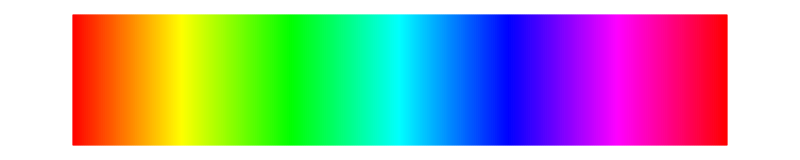

```mathematica
specLine
```

Like all local operators, binary morphological operators may be implemented using convolution-like algorithms (where the fundamental operations of addition and multiplication of standard convolution are replaced with logical ORs and ANDs), though they can also be thought of as operations on sets. The two basic morphological operations are dilation and erosion, and most of the more advanced morphological functions are combinations of these two. In the figure below, the image f is assumed to be binary, and the neighborhood is shown as a 3x3. The basic form of both erosion and dilation is to combine the 0-1's in the neighborhood using logical operations.

```mathematica
Labeled[GraphicsRow[{-Graphics-},ImageSize->400] ,"A morphological operation operates on a binary image by combining all pixels in a specified neighborhood",LabelStyle->captionStyle](* 2dimMorphology.ai *)
```

-Graphics-A morphological operation operates on a binary image by combining all pixels in a specified neighborhood

### Erosion and Dilation

Each binary morphological operator is defined by a neighborhood (variously called a structuring element, a kernel, or a mask) and a logical operation that combines the elements of the image throughout the neighborhood. In the erosion operation, the elements are combined by logical AND; the output g(x,y) of the morphological operation at the point (x,y) is the AND of all the pixel values. In words, the output is “1” if every point in the neighborhood is “1” and is zero otherwise. In the dilation operation, the elements are combined by logical OR; the output g(x,y) of the morphological operation at the point (x,y) is the OR of all the pixel values. In words, the output is “1” if any point in the neighborhood is “1” and is zero otherwise.

```mathematica
labelErodeDilateBW="The dilation (left) and erosion (right) of a binary image (middle)";
infoErodeDilateBW="Dilation makes the white circles larger; erosion makes them smaller.\n\nMove the neighborhood size all the way to the left, the dilation and erosion are almost indistinguishable.\n\nMove the neighborhood size all the way to the right: the dilation grows and the erosion shrinks.\n\nClick 'New Image' a few times to view the effects on a variety of synthetic images.\n\nChoose the shape to be a horizontalMatrix and observe how the dilation and erosion are shaped horizontally.\n\nTry the other shapes. Can you guess what the CrossMatrix will do?";
Manipulate[If[rd==1,setToOne=Round[Abs[RandomVariate[NormalDistribution[100/2,100/4],{8,2}]]];
synImg=Dilation[Graphics[{White,Point[setToOne]},Background->Black],DiskMatrix[60]];
If[RandomInteger[]==1,synImg=RangeFilter[synImg,10];];rd=0;];
GraphicsRow[{Dilation[synImg,neighborhood[r]],synImg,Erosion[synImg,neighborhood[r]]},ImageSize->800],{{rd,1,""},Button["New Image",rd=1]&},
Row[{Control[{{neighborhood,DiskMatrix,"neighborhood shape"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,inverseCrossMatrix,verticalMatrix,horizontalMatrix,DiamondMatrix}}],Spacer[30],Control[{{r,20,"neighborhood size"},1,60,1}],Spacer[20],info[infoErodeDilateBW]}],FrameLabel->Style[labelErodeDilateBW,Medium],TrackedSymbols->{r,rd,neighborhood},SaveDefinitions->True]
```

HW: In the code above, the figures are generated (somewhat randomly) by placing a set of white points on a black background and then dilating (with a DiskMatrix structuring element). Change the code to dilate with one of the other neighborhoods (IdentityMatrix, BoxMatrix, CrossMatrix, inverseCrossMatrix, verticalMatrix, horizontalMatrix, or DiamondMatrix) and explain the differences in the generated figures.

Dilation tends to make the white blobs larger (and the black areas smaller) while erosion tends to make the white areas smaller (and the black areas larger).

### Closing and Opening

It is common to use morphological operations in sequence to accomplish various tasks. The simplest sequence, called a closing, is to use a dilation followed by an erosion. The opposite sequence (an erosion followed by a dilation) is called an opening.

```mathematica
labelCloseOpenBW="The opening (left) and closing (right) of a binary image";
infoCloseOpenBW="Closing tends to remove small black features (such as the centers of the circles).\n\nOpening tends to retain white centers (larger than the neighborhood) while removing surrounding matter.\n\nTry different neighborhood shapes.\n\nClosing tends to merge together object that are close together.\n\nOpening tends to separate white objects that are narrower than the neighborhood.";
Manipulate[If[rd==1,setToOne=Round[Abs[RandomVariate[NormalDistribution[100/2,100/4],{8,2}]]];
synOpImg=Graphics[Table[{White,Disk[setToOne[[i]],RandomInteger[{8,20}]],Black,Disk[setToOne[[i]],3]},{i,1,Length[setToOne]}],Background->Black];
If[RandomInteger[]==1,synOpImg=RangeFilter[synOpImg,10];];rd=0;];
GraphicsRow[{Opening[synOpImg,neighborhood[r]],synOpImg,Closing[synOpImg,neighborhood[r]]},ImageSize->800],{{rd,1,""},Button["New Image",rd=1]&},
Row[{Control[{{neighborhood,DiskMatrix,"neighborhood shape"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,inverseCrossMatrix,verticalMatrix,horizontalMatrix,DiamondMatrix}}],Spacer[30],Control[{{r,20,"neighborhood size"},1,60,1}],Spacer[20],info[infoCloseOpenBW]}],FrameLabel->Style[labelCloseOpenBW,Medium],TrackedSymbols->{r,rd,neighborhood},SaveDefinitions->True]
```

Closing tends to remove small black features (such as the centers of the circles) while opening tends to retain white centers while removing surrounding matter.

### Grayscale Morphology

In binary dilation, an output pixel is “1” if any of the elements in its neighborhood are “1” (i.e., logical OR). Another way of saying this is that the output pixel takes on the maximum value of all the (binary) pixels in the neighborhood. Similarly, in binary erosion, an output pixel is “1” only when all of the elements in its neighborhood are “1” (i.e., logical AND). An equivalent way of saying this is that the output pixel takes on the minimum value of all the (binary) pixels in the neighborhood. Accordingly, a simple way to generalize binary morphological operations to grayscale images is to use the MaxFilter[ ] and MinFilter[ ]. In one dimension, the only variable is the width of the neighborhood.

```mathematica
labelGrayMorph="A single row from a thread x-ray is green, the dilation (max filter) is blue, the erosion (min filter) is red, the closing is orange and the opening is black";
infoGrayMorph="Consider rows from a thread x-ray as 1D functions (the green cruves).\n\nSweep through the rows and observe that the red and blue curves (the erosion and dilation) form lower and upper bounds for the function.\n\nSweep through the rows and observe that the black and orange curves (the opening and closing) also form lower and upper bounds for the function.\n\nTurn the neighborhood size down to 4 and observe that the bounds tighten: the red and blue always keep a certain horizontal distance from green, while the orange and black bounds cling tightly to the green near the peaks and valleys.\n\nTurn the neighborhood size up, observe the bounds loosen.";
imgData=ImageData[allImagesXray[[f634Tile]]][[1;;100,1;;100]];
Manipulate[imgRow=imgData[[thisRow]];
GraphicsRow[{Show[Image[imgData,ImageSize->250],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{0,100-thisRow},{100,100-thisRow}}]}]],ListLinePlot[{imgRow, max=MaxFilter[imgRow, neigh],min=MinFilter[imgRow,neigh]}, 
    PlotRange -> {0,1}, PlotStyle->{{Thick,Green},Blue,Red},ImageSize -> 300],
ListLinePlot[{imgRow,MinFilter[max,neigh],MaxFilter[min,neigh]},PlotRange->{0,1},PlotStyle->{{Thick,Green},Orange,Black},ImageSize->300]}],
Row[{Control[{{thisRow,27,"row from canvas"},1,100,1}],Spacer[20],Control[{{neigh,12,"neighborhood size"}, 1,  21, 1,Appearance->"Labeled"}],Spacer[20],info[infoGrayMorph]}],
FrameLabel->Style[labelGrayMorph,Medium],TrackedSymbols->{thisRow,neigh},SaveDefinitions->True]
```

HW: Yet another way to implement the application of morphological operations to grayscale images is to use ListConvolve[ ]. Using these ideas, reimplement the above demonstration using ListConvolve[ ] and/or ListCorrelate[ ]. (In fact, this shows how many seemingly disparate functions such as MaxFilter[ ], MinFilter[ ], Erosion[ ], Dilation[ ], and ImageFilter[ ] are all just specific calls to ListConvolve[ ] and/or ListCorrelate[ ]). Describe your observations, and show how MaxFilter can be

```mathematica
specLine
```

-Graphics-

In one dimension, a neighborhood is just a distance along the axis. In two dimensions there is more flexibility in the shape of the neighborhoods.

```mathematica
labelXRayMorph="Applying various morpholological operations to x-ray images";
infoXRayMorph="When looking at individual threads, it makes sense to keep the neighborhood size small (since once the neighborhood is larger than the feature, important details are invariably lost).\n\nObserve that dilation of the positive image is the same as the negative of the eroded negative image.\n\nWhat is the same as erosion operating on the positive image? Can you explain why?\n\nSet the shape to verticalMatrix and the size to 40. Now all four operators emphasize the vertical stripes.\n\nFind a way to emphasize the horizontal stripes.\n\nUse the crossMatrix to bring out both vertical and horizontal features simultaneously.";
Manipulate[Module[{img},
If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
ImageAdjust[operation[img,neighborhood[rad]]]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],
Control[{{invert,"negative",""},{"negative","positive"}}]}],{{operation,Dilation,"operation"},{Dilation->"dilation",Erosion->"erosion",Opening->"opening",Closing->"closing"}},{{neighborhood,IdentityMatrix,"neighborhood shape"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,inverseCrossMatrix,verticalMatrix,horizontalMatrix,DiamondMatrix}},Row[{Control[{{rad,5,"neighborhood size"},1,80,1,Appearance->"Labeled"}],Spacer[10],info[infoXRayMorph]}],FrameLabel->Style[labelXRayMorph,Medium],TrackedSymbols->{i,invert,operation,rad,neighborhood},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

When applying the morphological operations to color images, the simplest approach is to apply the filters to each of the red, green, and blue channels separately. This may have the effect of changing the colors.

```mathematica
labelColorMorph="Applying various morphological operations to color images";
infoColorMorph="Unpredictable color changes are one of the reasons morphological operators tend to find most use in binary and grayscale images.\n\nExample: observe the blanket in the bedroom scene.\n\nAs expected, dilation tends to brighten while erosion tends to darken the image (try increasing the neighborhood to emphasize these effects).\n\nThe neighborhood shape influences the way the colors smear (compare box to cross to horizontal).";
Manipulate[Module[{img},img=allImagesColor[[i]];
Image[ImageAdjust[operation[img,neighborhood[nRad]]],ImageSize->400]],{{i,vanPlough,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu},{{operation,Dilation,"operation"},{Dilation->"dilation",Erosion->"erosion",Opening->"opening",Closing->"closing"}},{{neighborhood,CrossMatrix,"neighborhood shape"},{IdentityMatrix,DiskMatrix,BoxMatrix,CrossMatrix,inverseCrossMatrix,verticalMatrix,horizontalMatrix,DiamondMatrix}},
Row[{Control[{{nRad,19,"neighborhood size"},1,80,1,Appearance->"Labeled"}],Spacer[10],info[infoColorMorph]}],FrameLabel->Style[labelColorMorph,Medium],TrackedSymbols->{i,invert,operation,nRad,neighborhood},SaveDefinitions->saveDef]
```

HW: It is sometimes advantageous to conduct morphological operations on color images in the HSB colorspace. Generally, one applies the filters to the brightness channels, leaving the hue and saturation unchanged. Create a demonstration like the above that operates only on the brightness channel.

### Combining Morphological Operations

The fundamental operators of mathematical morphology can be combined and iterated to implement several useful image processing tasks, from edge and zero crossing detection, thinning and pruning, to filling and reconstruction.

### Borders and Edges

Borders of objects in binary images and edges in grayscale images are commonly of interest in image processing. The morphological operations of erosion and dilation may be used to detect borders and edges in a straightforward way. Recall that dilation expands the edges of a binary shape by an amount proportional to the size of the structuring element. Taking the dilated image and subtracting the original leaves only the expanded area; this is called the outer boundary. Similarly, erosion shrinks all edges of a binary shape. Subtracting the erosion from the original leaves an inner border called the inner boundary. A third variation is to subtract the erosion from the dilation to get the double boundary.

```mathematica
labelBorders="The image (top left), outer boundary (top right), inner boundary (bottom left) and double boundary";
infoBorders="Change the neighborhood size to make the boundaries thicker or thinner.\n\nThe double bounday is thicker than either the inner or outer boundary.\n\nTry several 'new images' to see the fidelity of the boundaries.";
Manipulate[If[rd==1,setToOne=Round[Abs[RandomVariate[NormalDistribution[100/2,100/4],{8,2}]]];
synBorImg=Dilation[Graphics[{White,Point[setToOne]},Background->Black],DiskMatrix[60]];
If[RandomInteger[]==1,synBorImg=RangeFilter[synBorImg,10];];
rd=0;];
GraphicsGrid[{{synBorImg,ImageSubtract[Dilation[synBorImg,bRad],synBorImg]},{ImageSubtract[synBorImg,Erosion[synBorImg,bRad]],ImageSubtract[Dilation[synBorImg,bRad],Erosion[synBorImg,bRad]]}},ImageSize->500],
Row[{Control[{{rd,1,""},Button["New Image",rd=1]&}],Spacer[30],Control[{{bRad,3,"neighborhood size"},1,6,1,Appearance->"Labeled"}],Spacer[20],info[infoBorders]}],FrameLabel->Style[labelBorders,Medium],TrackedSymbols->{rd,bRad},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

The boundary finding operations can be used to find boundaries of grayscale and color images in the same way. While all three boundaries are basically the same in the binary case (except for the width) the boundaries can vary substantially when applied to grayscale and color images.

```mathematica
labelBordersBW="The three boundary operations applied to binary, grayscale and color images";
infoBordersBW="Compare the boundaries of binary, grayscale, and color images.\n\nThe threshold only has effect in the binary case. Observe how different threshold values bring out different portions of the image.\n\nThe identity/invert button inverts the output to show black edges on a white background (rather than white edges on a black background).\n\nFor grayscale, the double boundary is brighter than the inner or outer, but may have a ghosting effect.\n\nWhen applied to color images, the boundaries may take on the color of the surrounding image. What does this suggest about the implementation?\n\nMake the bedroom scene look like a pencil sketch (color/invert/size=8)\n\nMake the bedroom scene look like a watercolor (color/identity/size=25)";
Manipulate[Module[{img},Which[color=="color",img=allImagesColor[[i]];,
color=="grayscale",img=ColorConvert[allImagesColor[[i]],"Grayscale"];,
color=="binary",img=Binarize[allImagesColor[[i]],t]];
If[invert=="identity",negate=Identity,negate=ColorNegate];
GraphicsGrid[{{img,negate[ImageSubtract[Dilation[img,bRadius],img]]},{negate[ImageSubtract[img,Erosion[img,bRadius]]],negate[ImageSubtract[Dilation[img,bRadius],Erosion[img,bRadius]]]}},ImageSize->700]],Row[{Control[{{i,vermeerMilk,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20] ,Control[{{color,"grayscale",""},{"binary","grayscale","color"}}],Spacer[20],Control[{{invert,"identity",""},{"identity","invert"}}],Spacer[20],info[infoBordersBW]}],
Row[{Control[{{t,0.5,"binarization threshold"},0,1}],Spacer[20],Control[{{bRadius,3,"neighborhood size"},1,30,1,Appearance->"Labeled"}]}],FrameLabel->Style[labelBordersBW,Medium],TrackedSymbols->{i,color,bRadius,t,invert},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

The three boundary operations are also called the morphological gradients because they are large when the signal changes rapidly and small when the signal changes only slightly. It is perhaps easier to see the qualitative relationship with the gradient (derivative) when the signal is one-dimensional.

```mathematica
labelBoundary1D="A single row from a thread x-ray is green, the outer boundary in blue, inner boundary in red, and double boundary in black";
infoBoundary1D="For small neighborhood sizes, morphological boundaries are similar to gradients (derivatives) because they are large when the signal varies and small when it is constant.\n\nLook at a number of rows and observe that the double boundary is the sum of the inner and the outer boundaries.\n\nWhich of the boundaries is closest to the actual gradient (actually, to the Abs[] of the gradient)? What neighborhood size is needed?\n\nFor large sizes, the double boundary has large flat regions. Why is this?";
imgData=ImageData[allImagesXray[[f634Tile]]][[1;;100,1;;100]];
Manipulate[imgRow=imgData[[thisRow]];
GraphicsRow[{Show[Image[imgData,ImageSize->250],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{0,100-thisRow},{100,100-thisRow}}]}]],ListLinePlot[{imgRow,outerB (MaxFilter[imgRow,r]-imgRow),innerB (imgRow-MinFilter[imgRow,r]),doubleB (MaxFilter[imgRow,r]-MinFilter[imgRow,r]),grad Abs[Differences[imgRow]]},PlotRange->{0,1},PlotStyle->{{Thick,Green},Blue,Red,Black,{Thick,Orange}},AspectRatio->1,ImageSize->300]}],
Control[{{thisRow,27,"row from canvas"},1,100,1}],Row[{Control[{{innerB,1,"display inner boundary"},{0,1}}],Control[{{outerB,1,"   outer boundary"},{0,1}}],Control[{{doubleB,1,"   double boundary"},{0,1}}],Control[{{grad,0,"   gradient"},{0,1}}]}],Row[{Control[{{r,5,"neighborhood size"},1,21,1,Appearance->"Labeled"}],Spacer[20],info[infoBoundary1D]}],FrameLabel->Style[labelBoundary1D,Medium],TrackedSymbols->{thisRow,r,grad,innerB,outerB,doubleB},SaveDefinitions->True]
```

### Detecting Peaks and Valleys

Morphological filters can be used to detect peaks and valleys in grayscale images. The tophat filter, which enhances positive peaks, is the difference between the original image and its opening. The tophat filter extracts white peaks that are smaller than the size of the structuring element.

```mathematica
labelPeaks="The image (left), its opening (middle), and the tophat filter (difference between the image and its opening)";
infoPeaks="Compare the opening and the tophat filter of binary, grayscale, and color images.\n\nThe threshold only has effect in the binary case. Observe how different threshold values bring out different portions of the image.\n\nThe opening is boxy because the structuring element is (by default) a square.\n\nFor example, in the bedroom, (color, size=25) the walls of the room take on interesting color variations.\n\nAs the neighborhood increases, the effect approaches that of the difference between the image and its mean. For smaller sizes, it is like the difference between the image and its local mean.";Manipulate[Module[{img},Which[color=="color",img=allImagesColor[[i]];,color=="grayscale",img=ColorConvert[allImagesColor[[i]],"Grayscale"];,color=="binary",img=Binarize[allImagesColor[[i]],t]];
Row[{Image[img,ImageSize->150],Image[Opening[img,pRad],ImageSize->350],Image[ImageAdjust[TopHatTransform[img,pRad]],ImageSize->350]}]],Row[{Control[{{i,vermeerMilk,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],Control[{{color,"color",""},{"binary","grayscale","color"}}],Spacer[20],Control[{{pRad,13,"neighborhood size"},1,50,1,Appearance->"Labeled"}]}],
Row[{Control[{{t,0.5,"binarization threshold"},0,1}],Spacer[20],info[infoPeaks]}],FrameLabel->Style[labelPeaks,Medium],TrackedSymbols->{i,color,pRad,t},SaveDefinitions->saveDef]
```

The same images result from using ImageSubtract[img, Opening[img, radius]] instead of the built in function TopHatTransform[img, radius].

```mathematica
specLine
```

-Graphics-

The bottom hat is the dual transformation, defined as the difference between the image and its closing. The bottom-hat preserves the valleys in the signal whose width is smaller than the structuring element.

```mathematica
labelBottomHat="The image (left), its closing (middle), and the tophat filter (difference between the image and its closing)";
infoBottomHat="Compare the closing and the tophat filter of binary, grayscale, and color images.\n\nThe threshold only has effect in the binary case. Observe how different threshold values bring out different portions of the image.\n\nThe closing is boxy because the structuring element is (by default) a square.\n\nThe Little Street turns from a cloudy day into an ominously lit night-time scene.\n\nAs the neighborhood increases, the effect approaches that of the difference between the image and its mean. For smaller sizes, it is like the difference between the image and its local mean.";;Manipulate[Module[{img},Which[color=="color",img=allImagesColor[[i]];,color=="grayscale",img=ColorConvert[allImagesColor[[i]],"Grayscale"];,color=="binary",img=Binarize[allImagesColor[[i]],t]];
Row[{Image[img,ImageSize->150],Image[Closing[img,hatRad],ImageSize->350],Image[ImageAdjust[BottomHatTransform[img,hatRad]],ImageSize->350]}]],Row[{Control[{{i,vermeerMilk,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],Control[{{color,"color",""},{"binary","grayscale","color"}}],Spacer[20],Control[{{hatRad,26,"neighborhood size"},1,50,1,Appearance->"Labeled"}]}],
Row[{Control[{{t,0.5,"binarization threshold"},0,1}],Spacer[20],info[infoBottomHat]}],FrameLabel->Style[labelBottomHat,Medium],TrackedSymbols->{i,color,hatRad,t},SaveDefinitions->saveDef]
```

HW: Create a 1D demonstration of the effect of either the tophat or the bottomhat transformations. Model your demonstration after the 1D demo of the morphological gradient.

HW: Apply either the tophat or the bottomhat filters to the x-ray canvas images.

### Morphological Skeletons

In many shape-based image analysis applications, the internal structure of the object is more interesting than its external structure. One way to represent internal structure is with a simplified line-representation called the morphological skeleton. The computation of the skeleton begins with the function

```mathematica
ImageSubtract[Erosion[image,r],Opening[Erosion[image,r],1]];
```

In words, the operation is to erode the image (with a structuring element of size r) and to then subtract the opening of that erosion. This is repeated for all r (up to some largest size). The skeleton is then the union (logical OR or binary sum) of all the results. Here the skeleton operation is applied to the circle-images.

```mathematica
labelSkeletonBW="The morphological skeleton reduces each white area to a single curve";
infoSkeletonBW="Look through several of the synthetic 'new images'. Observe that the skeleton is the central core of the shape.\n\nWhere the image has an isolated ring, the skeleton has a circle.\n\nWhere multiple rings touch, the skeleton circles join to form connected structures.";
Manipulate[If[rd==1,setToOne=Round[Abs[RandomVariate[NormalDistribution[100/2,100/4],{8,2}]]];
synMorphImg=RangeFilter[Dilation[Graphics[{White,Point[setToOne]},Background->Black],DiskMatrix[60]],10];rd=0;];
GraphicsRow[{synMorphImg,ImageAdjust[Image[Total[Table[ImageData[ImageSubtract[Erosion[synMorphImg,r],Opening[Erosion[synMorphImg,r],1]]],{r,1,20}]]]]},ImageSize->500],Row[{Control[{{rd,1,""},Button["New Image",rd=1]&}],Spacer[20],info[infoSkeletonBW]}],
FrameLabel->Style[labelSkeletonBW,Medium],SynchronousUpdating->False,TrackedSymbols->{rd},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

The morphological skeleton operation can also be applied to more interesting images. The built-in function Thinning[ ] can also be used to carry out the required erosions and openings.

```mathematica
labelThinningBW="The morphological skeleton reduces each white area to a single curve";
infoThinningBW="The skeleton/thinning process can be applied to more interesting shapes.\n\nThere are two methods to choose from, which give slightly different results.\n\nFor example: all the points of the umbrella appear when using the MedialAxis option while some are missing from the Morphological option.\n\nOn the other hand, the Morphological option gives a smoother represntation of the ψ symbol, without spikes leading out to the inflection points of the arms.";
Manipulate[GraphicsRow[{synSkelImg=ColorNegate[shapes[[i]]],ImageAdjust[Thinning[synSkelImg,Method->optThin]]},ImageSize->700],Row[{Control[{{i,4,"image"},Thread[Range[Length[shapes]]->shapes],ControlType->PopupMenu}],Spacer[20],Control[{{optThin,"Morphological",""},{"Morphological","MedialAxis"}}],Spacer[20],info[infoThinningBW]}],FrameLabel->Style[labelThinningBW,Medium],TrackedSymbols->{i,optThin},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Morphological skeletonization can also be applied to grayscale images. This interactive example compares the direct calculation of the skeleton with using the built-in function Thinning[ ].

```mathematica
labelMorphSkelXRay="Applying the morphological skeleton to canvas x-rays";
infoMorphSkelXRay="Two ways of implementing the skeleton: the Thinning[ ] command (which has no options) and the difference between the opening and the erosion, iterated several times.\n\nThere are advantages to each:\nIt's good to have no options becasue then there's no need to pick a parameter\nIt's better to have options because then you can tailor the results.\n\nApplied to F634, the method does a reasonable job separating out all the thread tops.\n\nIn some cases (for example, L10) it may be advantageous to work with the positive image (and to locate the holes in the thread) rather than with the negative (and locate the tops of the threads)";
Manipulate[Module[{img},If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
GraphicsRow[{img,ImageAdjust[Image[Total[Table[ImageData[ImageSubtract[Erosion[img,r],Opening[Erosion[img,r],1]]],{r,1,50}]]]],ImageAdjust[Thinning[img,10,t]]},ImageSize->900]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[30], Control[{{invert,"positive",""},{"negative","positive"}}],Spacer[30],Control[{{t,0.58,"threshold"},0,1}],Spacer[20],info[infoMorphSkelXRay]}],
FrameLabel->Style[labelMorphSkelXRay,Medium],TrackedSymbols->{i,invert,t},SynchronousUpdating->False,ContinuousAction->False,SaveDefinitions->saveDef]
```

HW: Mathematica also has a built-in function SkeletonTransform[ ]. Try using this in place of the morphological skeleton. Do you prefer SkeletonTransform[ ] for looking at canvas x-rays? Do you prefer it when applying to these shapes? Explain the reasons for your preferences.

```mathematica
shapes
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* One possible answer: Manipulate[Module[{img},If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
GraphicsRow[{img,ImageAdjust[SkeletonTransform[img,t]]},ImageSize->700]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[30] Control[{{invert,"positive",""},{"negative","positive"}}]}],{t,0,1},FrameLabel->Style["The morphological skeleton applied to canvas x-rays",Medium],TrackedSymbols->{i,invert,t},SaveDefinitions->saveDef] *)
```

### Ultimate Erosion

Dilation makes white objects larger; erosion makes them smaller. If an image is eroded, then eroded again and again, eventually there will be nothing left but black. Returning one step backwards (i.e., before the final erosion) only a single white point remains, the most central point in the object. The idea behind ultimate erosion is to erode each object to nothingness and then go one step backwards to return a single central point for each object. While ultimate erosion can be implemented exactly as described, there is a better way. Taking the distance transform creates a topographic surface of all the objects; the highest point in each connected surface is a central point. Accordingly, much the same method can arise by finding the maxima of the Distance transform.

```mathematica
labelUltimateErosion="Ultimate erosion (right) of a binary image (left) shows one point for each separated white ball";
infoUltimateErosion="Click to work with several synthetic 'new images.'\n\nObserve that the center of each circle is found by the ultimate erosion.\n\nWhen multiple circles overlap, there is often a dotted line of answers.";Manipulate[If[rd==1,setToOne=Round[Abs[RandomVariate[NormalDistribution[100/2,100/4],{RandomInteger[{3,10}],2}]]];
synSkelImg=Graphics[Table[{White,Disk[setToOne[[i]],RandomChoice[Range[5,20]]]},{i,1,Length[setToOne]}],Background->Black];rd=0;];
GraphicsRow[{synSkelImg,distImg=ImageAdjust[DistanceTransform[synSkelImg]],Dilation[MaxDetect[distImg],1]},ImageSize->800],Row[{Control[{{rd,1,""},Button["New Image",rd=1]&}],Spacer[20],info[infoUltimateErosion]}],FrameLabel->Style[labelUltimateErosion,Medium],TrackedSymbols->{rd},SaveDefinitions->True]
```